## Dataset Visualization

### Boolean Objects

```mathematica
booleanObjects=Import[FileNameJoin[{NotebookDirectory[],"Dataset","booleanData.json"}]];
booleanObjects=Association/@booleanObjects;
```

```mathematica
complexityData=SortBy[First][List@@@Normal[CountsBy[#["Complexity"]&][booleanObjects]]]
```

{{2,1},{3,6},{4,32},{5,121},{6,405},{7,1016},{8,2024},{9,3318},{10,4712},{11,6238},{12,7526},{13,9005},{14,10315},{15,11800},{16,12716},{17,13833},{18,14623},{19,15064},{20,14634},{21,14411},{22,13085},{23,12846},{24,10882},{25,10016},{26,9030},{27,9948},{28,8547},{29,9603},{30,8097},{31,8916},{32,7050},{33,7880},{34,6293},{35,6992},{36,5394},{37,6005},{38,4407},{39,4752},{40,3248},{41,3659},{42,2761},{43,2930},{44,2225},{45,2769},{46,1919},{47,2119},{48,1636},{49,1719},{50,1098},{51,1300},{52,902},{53,1396},{54,1233},{55,1297},{56,1008},{57,1268},{58,780},{59,869},{60,702},{61,954},{62,522},{63,662},{64,500},{65,654},{66,408},{67,488},{68,368},{69,510},{70,288},{71,408},{72,196},{73,403},{74,168},{75,256},{76,124},{77,123},{78,108},{79,188},{80,84},{81,176},{82,30},{83,148},{84,124},{85,184},{86,30},{87,56},{88,40},{89,64},{91,68},{92,48},{93,36},{94,48},{95,24},{96,16},{97,80},{99,86},{100,32},{101,32},{103,32},{105,88},{106,16},{107,16},{108,16},{109,64},{110,32},{111,60},{112,16},{113,80},{114,16},{115,48},{117,32},{119,16},{120,32},{121,112},{123,16},{124,16},{125,32},{126,48},{128,16},{129,48},{137,16},{169,64},{201,32}}

```mathematica
fig[0]=Block[{
data=List@@@Normal[Total/@GroupBy[
If[First[#]>=80,80,Floor[First[#],20]]&->Last][complexityData]],
legends
},
legends=Append[
Most[
MapThread[#1<>" ≤ complexity < "<>#2&,
Transpose[Partition[ToString@*First/@data,2,1,1]]
]
],
"complexity ≥ 80"
];
PieChart[data[[All,2]],
LabelingFunction->Function[
Callout[
ToString[Round[100#/Total[data[[All,2]]],1]]<>"%"
]
],
ChartLegends->Placed[legends,Right],
PlotTheme->"Scientific"
]
]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"BooleanObjectDatasetComplexityPieChart.pdf",fig[0]]
```

D:\本科毕设\Experiment\BooleanObjectDatasetComplexityPieChart.pdf

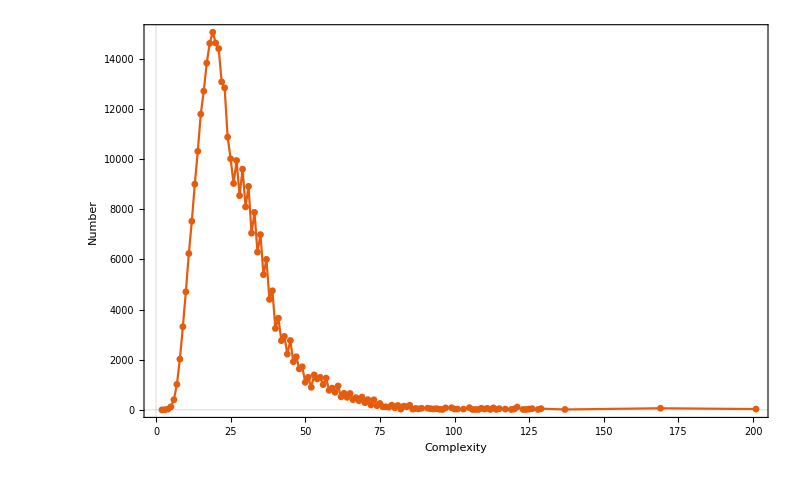

```mathematica
fig[1]=ListLinePlot[
complexityData,
PlotTheme->"Scientific",
PlotMarkers->{Automatic,Small},
FrameLabel->Map[Style[#,16]&,{"Complexity","Number"}],
Frame->True,
ImageSize->800
]
```

```mathematica
Export[NotebookDirectory[]<>"BooleanObjectDatasetComplexityDistribution.pdf",fig[1]]
```

D:\本科毕设\Experiment\BooleanObjectDatasetComplexityDistribution.pdf

### Direct Boolean Computation / Indirect Boolean Computation

```mathematica
directBooleanComputationSet=Import[FileNameJoin[{NotebookDirectory[],"Dataset","DirectBooleanComputation.json"}]];
```

```mathematica
CountsBy[Lookup[#,"Answer"]&][directBooleanComputationSet]
```

<|True→14705,False→15117|>

```mathematica
Function[bool,
complexityDataDBC[bool]=SortBy[First][List@@@Normal[CountsBy[Lookup[#,"Complexity"]&][Select[directBooleanComputationSet,Lookup[#,"Answer"]===bool&]]]]
]/@{False,True};
```

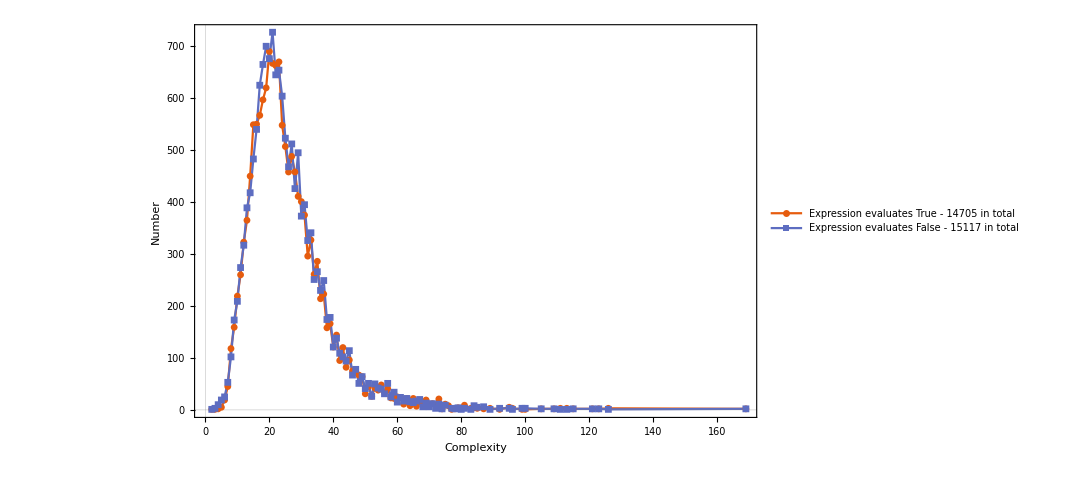

```mathematica
fig[2]=ListLinePlot[
{complexityDataDBC[True],complexityDataDBC[False]},
PlotTheme->"Scientific",
PlotMarkers->{Automatic,Small},
FrameLabel->Map[Style[#,16]&,{"Complexity","Number"}],
Frame->True,
ImageSize->800,
PlotLegends->Placed[Style[#,16]&/@{"Expression evaluates True - 14705 in total","Expression evaluates False - 15117 in total"},{Right,Top}]
]
```

```mathematica
indirectBooleanComputationSet=Import[FileNameJoin[{NotebookDirectory[],"Dataset","IndirectBooleanComputation.json"}]];
```

```mathematica
CountsBy[Lookup[#,"Answer"]&][indirectBooleanComputationSet]
```

<|True→13715,False→14145|>

```mathematica
Function[bool,
complexityDataIBC[bool]=SortBy[First][List@@@Normal[CountsBy[Lookup[#,"Complexity"]&][Select[indirectBooleanComputationSet,Lookup[#,"Answer"]===bool&]]]]
]/@{False,True};
```

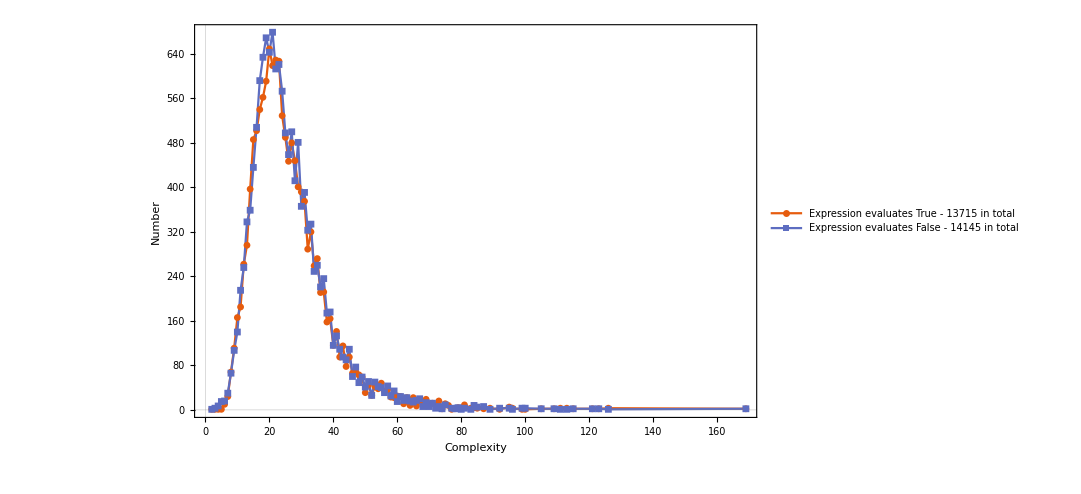

```mathematica
fig[3]=ListLinePlot[
{complexityDataIBC[True],complexityDataIBC[False]},
PlotTheme->"Scientific",
PlotMarkers->{Automatic,Small},
FrameLabel->Map[Style[#,16]&,{"Complexity","Number"}],
Frame->True,
ImageSize->800,
PlotLegends->Placed[Style[#,16]&/@{"Expression evaluates True - 13715 in total","Expression evaluates False - 14145 in total"},{Right,Top}]
]
```

```mathematica
MapThread[
Export[NotebookDirectory[]<>#1<>"BooleanComputationComplexityDistribution.pdf",#2]&,
{
{"Direct","Indirect"},
{fig[2],fig[3]}
}
]
```

{D:\本科毕设\Experiment\DirectBooleanComputationComplexityDistribution.pdf,D:\本科毕设\Experiment\IndirectBooleanComputationComplexityDistribution.pdf}

### CNF / DNF

```mathematica
MapThread[
Function[#2=Import[FileNameJoin[{NotebookDirectory[],"Dataset",#1<>".json"}]]],
{{"DNF","CNF"},{DNFdata,CNFdata}}
];
```

```mathematica
complexityDataBoolConv=SortBy[First][List@@@Normal[CountsBy[Lookup[#,"Complexity"]&][#]]]&/@{CNFdata,DNFdata};
```

```mathematica
complexityDataCNFRes=SortBy[First][List@@@Normal[Total/@GroupBy[
Function[exp,Count[ToExpression[exp],_Symbol|_String,Infinity,Heads->True]][#[[1]]]&->Last
][SortBy[First][List@@@Normal[CountsBy[Lookup[#,"Answer"]&][CNFdata]]]
]]];
```

Two datasets share same complexity

```mathematica
SameQ@@complexityDataBoolConv
```

True

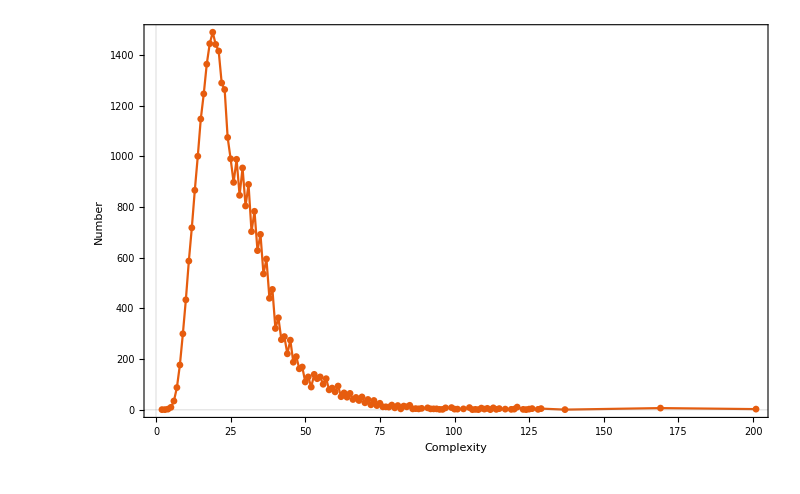

```mathematica
fig[4]=ListLinePlot[First[complexityDataBoolConv],
PlotTheme->"Scientific",
PlotMarkers->{Automatic,Small},
FrameLabel->Map[Style[#,16]&,{"Complexity","Number"}],
Frame->True,
ImageSize->800
]
```

```mathematica
Export[NotebookDirectory[]<>"BooleanConversionDist.pdf",fig[4]]
```

D:\本科毕设\Experiment\BooleanConversionDist.pdf

### TautologyQ / EquivalentQ

```mathematica
tautologyQSet=Import[FileNameJoin[{NotebookDirectory[],"Dataset","TautologyQ.json"}]];
```

```mathematica
CountsBy[Lookup[#,"TautologyQ"]&][tautologyQSet]
```

<|False→15037,True→15036|>

```mathematica
Function[bool,
complexityDataTQ[bool]=SortBy[First][List@@@Normal[CountsBy[Lookup[#,"Complexity"]&][Select[tautologyQSet,Lookup[#,"TautologyQ"]===bool&]]]]
]/@{False,True};
```

```mathematica
fig[5]=With[{number = Values[CountsBy[Lookup[#,"TautologyQ"]&][tautologyQSet]]},
PieChart[number,
ChartLegends->Placed[Map[Style[#,14,Bold]&,{"Not tautology","Tautology"}],Top],
ChartLabels->Map[Style[#,20]&,number]
]
]
```

-Graphics-

```mathematica
equivalentQSet=Import[FileNameJoin[{NotebookDirectory[],"Dataset","EquivalentQ.json"}]];
```

```mathematica
CountsBy[Lookup[#,"EquivalentQ"]&][equivalentQSet]
```

<|True→12420,False→12912|>

```mathematica
fig[6]=With[{number = Values[CountsBy[Lookup[#,"EquivalentQ"]&][equivalentQSet]]},
PieChart[number,
ChartLegends->Placed[Map[Style[#,14,Bold]&,{"Not equivalent","Equivalent"}],Top],
ChartLabels->Map[Style[#,20]&,number]
]
]
```

-Graphics-

```mathematica
MapThread[
Export[NotebookDirectory[]<>#1<>".pdf",#2]&,
{
{"TautologyQ-PieChart","EquivalentQ-PieChart"},
{fig[5],fig[6]}
}
]
```

{D:\本科毕设\Experiment\TautologyQ-PieChart.pdf,D:\本科毕设\Experiment\EquivalentQ-PieChart.pdf}

### SAT

```mathematica
SATSet=Import[FileNameJoin[{NotebookDirectory[],"Dataset","SAT.json"}]];
```

```mathematica
complexityDataSAT=SortBy[First][List@@@Normal[CountsBy[Lookup[#,"Complexity"]&][SATSet]]];
```

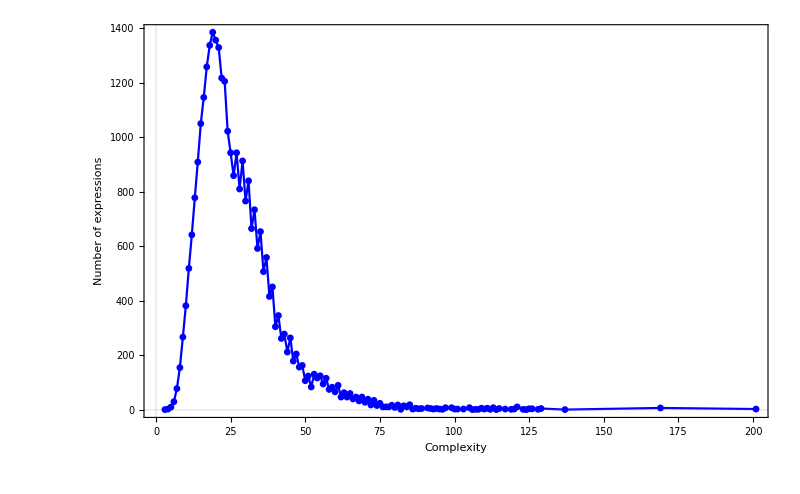

```mathematica
fig[7]=ListLinePlot[complexityDataSAT,
PlotTheme->"Scientific",
PlotMarkers->{Automatic,Small},
FrameLabel->Map[Style[#,16]&,{"Complexity","Number of expressions"}],
Frame->True,
ImageSize->800,
PlotStyle->Blue
]
```

```mathematica
Export[NotebookDirectory[]<>"SAT-Complexity-Distribution.pdf",fig[7]]
```

D:\本科毕设\Experiment\SAT-Complexity-Distribution.pdf

### #SAT

```mathematica
SATCountSet=Import[FileNameJoin[{NotebookDirectory[],"Dataset","SATCount.json"}]];
```

```mathematica
complexityDataSATCount=SortBy[First][List@@@Normal[CountsBy[Lookup[#,"Complexity"]&][SATCountSet]]];
```

```mathematica
fig[8]=ListPlot[
Lookup[SATCountSet,{"Complexity","Answer"}],
PlotStyle->Directive[PointSize[0.006]],
ImageSize->800,
Ticks->{Automatic,Range[1,14]},
ColorFunction->Hue,
FrameLabel->{Style["Complexity",16], Style["Number of satisfying assignments ",16]},
Frame->True,
PlotTheme->"Scientific",
PlotRange->{{0,150},Automatic}
]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"SATCount-Complexity-SolutionNum-Distribution.pdf",fig[8]]
```

D:\本科毕设\Experiment\SATCount-Complexity-SolutionNum-Distribution.pdf

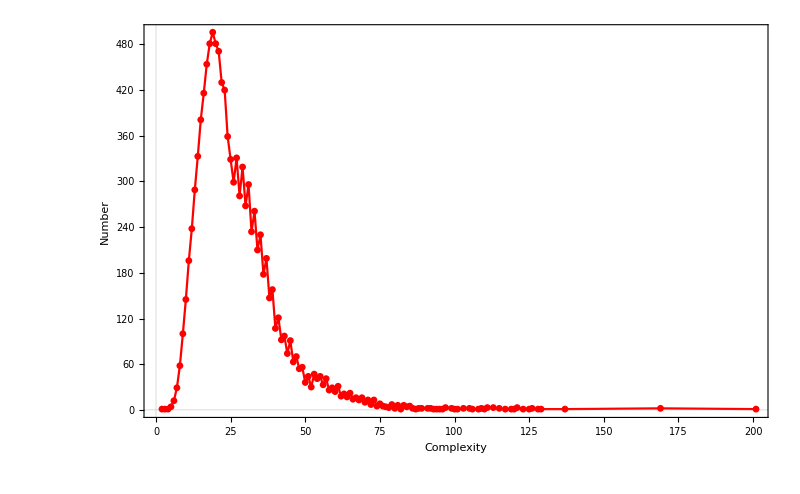

```mathematica
fig[9]=ListLinePlot[complexityDataSATCount,
PlotTheme->"Scientific",
PlotMarkers->{Automatic,Small},
FrameLabel->Map[Style[#,16]&,{"Complexity","Number"}],
Frame->True,
ImageSize->800,
PlotStyle->Red
]
```

```mathematica
Export[NotebookDirectory[]<>"SATCount-Complexity-Distribution.pdf",fig[9]]
```

D:\本科毕设\Experiment\SATCount-Complexity-Distribution.pdf